# PRACTICAL 1 : SOLUTION OF FIRST ORDER DIFFERENTIAL EQUATION

```mathematica
x=.
y=.
z=.
```

Plot and solve first order Differential equation

### Ques 1 : Solve y’ = y

```mathematica
sol1=DSolve[{y'[x]==y[x]},y[x],x]
```

{{y[x]→ⅇ^x C[1]}}

```mathematica
A=y[x]/.sol1/.{C[1]->1}
```

{ⅇ^x}

```mathematica
y[x]
```

y[x]

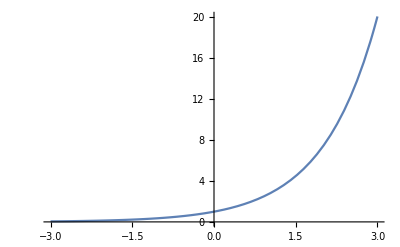

```mathematica
Plot [{A},{x,-3,3}]
```

Straight Integration

```mathematica
x=.
y=.
ClearAll
```

ClearAll

### Ques 2 : Solve y' = x^2

```mathematica
sol2=DSolve[y'[x]==x^2,y[x],x]
```

{{y[x]→x^3/3+C[1]}}

```mathematica
B1=y[x]/.sol2/.{C[1]->2}
```

{2+x^3/3}

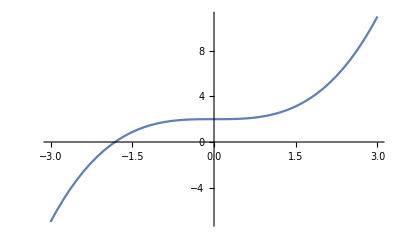

```mathematica
Plot[B1,{x,-3,3}]
```

```mathematica
Another Method
```

```mathematica
B2=Table[y[x]/.sol2/.{C[1]->k},{k,2,5}]
```

{{2+x^3/3},{3+x^3/3},{4+x^3/3},{5+x^3/3}}

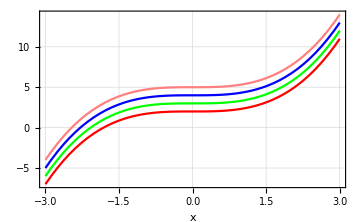

```mathematica
Plot[B2, {x,-3,3}, PlotStyle-> {Red, Green, Blue , Pink}, GridLines -> Automatic, Frame -> True, AxesOrigin->{0,0}, AxesLabel->Automatic, ImageSize->Medium]
```

```mathematica
Separable Equations
```

```mathematica
The general solution to this equation is found by separation of variable:
```

### Ques 3 : Solve y' = 2 xy

```mathematica
A=DSolve[y'[x]== 2*x*y[x]/(x+1), y[x], x]
```

{{y[x]→ⅇ^(2 (x-Log[1+x])) C[1]}}

```mathematica
B1=Table[y[x]/.A/.{C[1]->k}, {k,2,5}]
```

{{2 ⅇ^(2 (x-Log[1+x]))},{3 ⅇ^(2 (x-Log[1+x]))},{4 ⅇ^(2 (x-Log[1+x]))},{5 ⅇ^(2 (x-Log[1+x]))}}

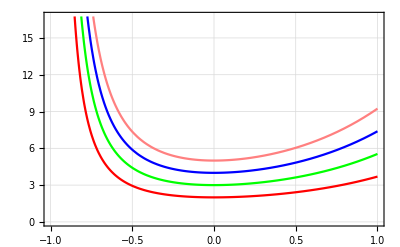

```mathematica
Plot[{B1}, {x,-1,1}, PlotStyle->{Red, Green, Blue, Pink}, GridLines-> Automatic, Frame->True, AxesOrigin->{0,0}]
```

```mathematica
Initial Value Problem
```

```mathematica
The solution of this type differential equations does not contain constant.
```

### Ques 4 : Solve y' = y + 2/xy, y[1] = 1

```mathematica
sol2=DSolve[{y'[x] == y[x]+2/x * y[x], y[1]==1}, y[x], x]
```

{{y[x]→ⅇ^(-1+x) x^2}}

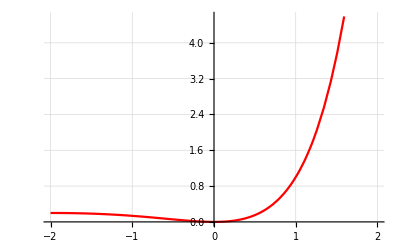

```mathematica
Plot[y[x]/.sol2, {x,-2,2}, PlotStyle->{Red}, GridLines-> Automatic]
```

```mathematica
Homogenous Equations
```

```mathematica
Here is a homogenous equation in which the total degree of both the numerator and the denominator of the righthand side is name. The two parts of the solution list give branches of the integral curves in the form :
```

### Ques 5 : Solve y' = x + y/y

```mathematica
sol3=DSolve[y'[x]== (x+y[x])/(x), y[x], x]
```

{{y[x]→x C[1]+x Log[x]}}

```mathematica
sol4=Table[y[x]/.sol3/.{C[1]-> k}, {k,2,5}]
```

{{2 x+x Log[x]},{3 x+x Log[x]},{4 x+x Log[x]},{5 x+x Log[x]}}

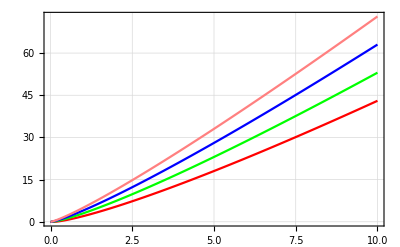

```mathematica
Plot[{sol4},{x,0,10}, PlotStyle->{Red, Green, Blue , Pink}, GridLines->Automatic, Frame->True, AxesOrigin->{0,0}]
```

```mathematica
Linear First-Order Equations
```

### Ques 6 : Solve y’ + y/(x) = x^2

```mathematica
sol5=DSolve[y'[x]+y[x]/(x) ==x^2, y[x], x]
```

{{y[x]→x^3/4+C[1]/x}}

```mathematica
sol6=Table[y[x]/. sol5/. {C[1]->k}, {k,2,5}]
```

{{2/x+x^3/4},{3/x+x^3/4},{4/x+x^3/4},{5/x+x^3/4}}

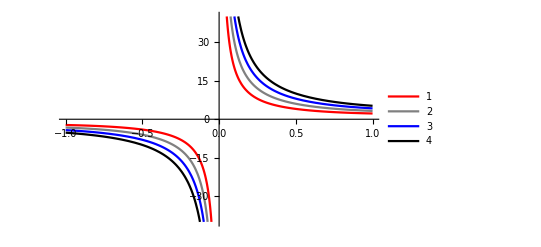

```mathematica
Plot[{sol6}, {x,-1,1}, PlotStyle->{Red, Gray, Blue, Black}, PlotLegends -> Automatic]
```

```mathematica
Plot[{sol6}, {x,-1,1}, PlotStyle->{Red, Gray, Blue, Black}, PlotLegends->Placed[Automatic, Below]]
```

-Graphics-

### Ques 7 : y'*tan (x) = 2 y - 8, y[Pi/2] = 0

```mathematica
sol7=DSolve[{y'[x]*Tan[x]==2*y[x]-8, y[Pi/2]==0}, y[x], x]
```

{{y[x]→-4 (-1+Sin[x]^2)}}

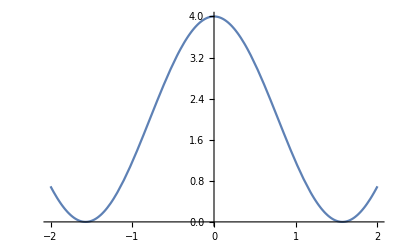

```mathematica
Plot[y[x]/.sol7, {x,-2,2}]
```

```mathematica
Bernoulli Equations
```

### Ques 8 : Solve x*y' + y = y^2*x^2 + 1

```mathematica
sol8=DSolve[x*y'[x]+y[x]== y[x]^2x^2+1, y[x], x]
```

{{y[x]→Tan[x+C[1]]/x}}

```mathematica
sol9=Table[y[x]/.sol8/.{C[1]->k}, {k,1,4}]
```

{{Tan[1+x]/x},{Tan[2+x]/x},{Tan[3+x]/x},{Tan[4+x]/x}}

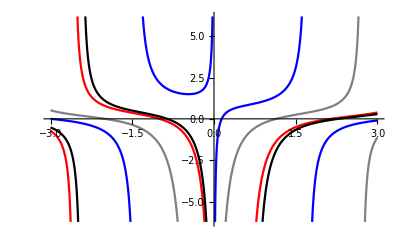

```mathematica
Plot[{sol9}, {x,-3,3}, PlotStyle->{Red, Gray, Blue, Black}, PlotLegends->Placed["Ëxpressions", Right]]
```

```mathematica
Exact Equations
```

### Ques 9 : Classify the differential equation as exact or not D[f (x, y), differentiate with respect to] D[f (x, y), x] diff wrt x (xy^2 + x) dx + (yx^2) dy = 0

```mathematica
M1[x_, y_] := (x*y^2+x)
```

```mathematica
N1[x_, y_] := (y*x^2)
```

```mathematica
Simplify[D[M1[x,y],y] - D[N1[x,y],x]]
```

0

```mathematica
eqn=y'[x] == -M1[x,y[x]]/N1[x,y[x]]
```

y'[x]==(-x-x y[x]^2)/(x^2 y[x])

```mathematica
sol11=DSolve[eqn, y[x],x]
```

{{y[x]→-(√(ⅇ^(2 C[1])-x^2))/x},{y[x]→(√(ⅇ^(2 C[1])-x^2))/x}}

```mathematica
p[x_, y_] := -(5x^2 - 2y^2+11)
```

```mathematica
q[x_,y_] := (Sin[y]+4x*y+3)
```

```mathematica
Simplify[D[p[x,y],y]-D[q[x,y],x]]
```

0

### Ques 10 : (3 x + 2 y) dx + (2 x + y) dy = 0

```mathematica
p[x_,y_]:=(3x+2y)
q[x_,y_]:=(2x+y)
Simplify[D[p[x,y],y]-D[q[x,y],x]]
```

0

### Ques 11 : (y^2 + 3) dx +(2 x y -4) dy = 0

```mathematica
p[x_,y_]:=(y^2+3)
q[x_,y_]:=(2x*y-4)
Simplify[D[p[x,y],y]-D[q[x,y],x]]
```

### Ques 12 : (4 x +3 y^2) dx + (2 xy) dy = 0

```mathematica
p1[x_,y_]:=(4x+3y^2)
q1[x_,y_]:=(2x*y)
Simplify[D[p[x,y],y]-D[q[x,y],x]]
```

0

# PRACTICAL 2 : SECOND ORDER DIFFERENTIAL EQUATION

Homogeneous Linear ODEs of Second Order

```mathematica
Real and Distinct
```

### Ques 1 : y’’ + 5y’ - 6y = 0

```mathematica
sol=DSolve[y''[x]+5y'[x]-6y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(-6 x) C[1]+ⅇ^x C[2]}}

```mathematica
sol1=y[x]/.sol[[1]]/.{C[1]->2,C[2]->7}
```

2 ⅇ^(-6 x)+7 ⅇ^x

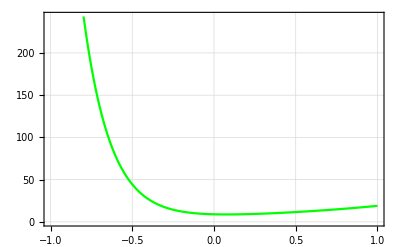

```mathematica
Plot[{sol1},{x,-1,1},PlotStyle->{Green},Frame->True,AxesOrigin->{0,0},GridLines->Automatic]
```

```mathematica
Ques 2: y''+y=0
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

{Cos[x]+2 Sin[x]}

{Cos[x]+3 Sin[x]}

{Cos[x]+4 Sin[x]}

{Cos[x]+5 Sin[x]}

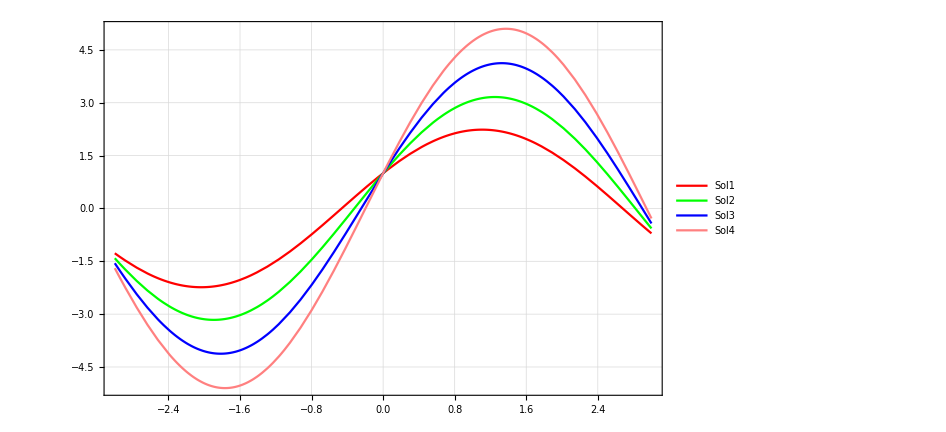

```mathematica
Sol=DSolve[y''[x]+y[x]==0,y[x],x]
Sol1= y[x]/.Sol/.{C[1]->1,C[2]->2}
Sol2= y[x]/.Sol/.{C[1]->1,C[2]->3}
Sol3= y[x]/.Sol/.{C[1]->1,C[2]->4}
Sol4= y[x]/.Sol/.{C[1]->1,C[2]->5}
Plot[{Sol1,Sol2,Sol3, Sol4},{x,-3,3},PlotStyle->{Red,Green,Blue,Pink},
Frame->True,AxesOrigin->{0,0},GridLines->Automatic,ImageSize->700,PlotLegends->LineLegend[{"Sol1","Sol2","Sol3","Sol4"},LegendFunction->"Frame"]]
```

```mathematica
Real and Equal Roots
```

```mathematica
Ques 3 : y''-6y'+9y=0
```

```mathematica
sol2=DSolve[y''[x]-6y'[x]+9y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(3 x) C[1]+ⅇ^(3 x) x C[2]}}

```mathematica
sol3=y[x]/.sol2[[1]]/.{C[1]->2,C[2]->3}
```

2 ⅇ^(3 x)+3 ⅇ^(3 x) x

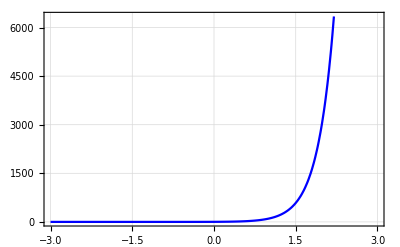

```mathematica
Plot[{sol3},{x,-3,3},PlotStyle->{Blue},Frame->True,AxesOrigin->{0,0},GridLines->Automatic]
```

```mathematica
Ques 4: 4y''+12y'+9y=0
```

```mathematica
B=DSolve[4y''[x]+12y'[x]+9y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(-3 x/2) C[1]+ⅇ^(-3 x/2) x C[2]}}

```mathematica
B1=Table[y[x]/.B/.{C[1]->2,C[2]->k},{k,2,5}]//TableForm
```

2 ⅇ^(-3 x/2)+2 ⅇ^(-3 x/2) x
2 ⅇ^(-3 x/2)+3 ⅇ^(-3 x/2) x
2 ⅇ^(-3 x/2)+4 ⅇ^(-3 x/2) x
2 ⅇ^(-3 x/2)+5 ⅇ^(-3 x/2) x

```mathematica
Plot[B1,{x,-1,1},PlotStyle->{Red,Green,Blue,Pink},
Frame->True,AxesOrigin->{0,0},GridLines->Automatic,ImageSize->500,PlotLegends->LineLegend[{"Sol1","Sol2","Sol3","Sol4"},LegendFunction->"Frame"]]
```

-Graphics-

```mathematica
Imaginary Roots
```

```mathematica
Ques 5: 4y''-y'+y=0
```

```mathematica
sol4=DSolve[y''[x]-y'[x]+y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(x/2) C[1] Cos[(√3 x)/2]+ⅇ^(x/2) C[2] Sin[(√3 x)/2]}}

```mathematica
{{y[x]->ⅇ^(x/2) C[1] Cos[(√3 x)/2]+ⅇ^(x/2) C[2] Sin[(√3 x)/2]}}
```

{{y[x]→ⅇ^(x/2) C[1] Cos[(√3 x)/2]+ⅇ^(x/2) C[2] Sin[(√3 x)/2]}}

```mathematica
sol5=y[x]/.sol4[[1]]/.{C[1]->2,C[2]->3}
```

2 ⅇ^(x/2) Cos[(√3 x)/2]+3 ⅇ^(x/2) Sin[(√3 x)/2]

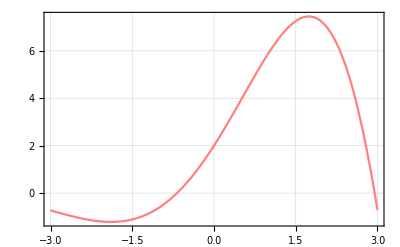

```mathematica
Plot[sol5,{x,-3,3},PlotStyle->{Red,Green,Blue,Pink},
Frame->True,AxesOrigin->{0,0},GridLines->Automatic]
```

```mathematica
Ques 6: y''-4y'+13y=0
```

```mathematica
c=DSolve[y''[x]-4y'[x]+13y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(2 x) C[2] Cos[3 x]+ⅇ^(2 x) C[1] Sin[3 x]}}

```mathematica
c1=Table[y[x]/.c/.{C[1]->k,C[2]->2},{k,3,6}]
```

{{2 ⅇ^(2 x) Cos[3 x]+3 ⅇ^(2 x) Sin[3 x]},{2 ⅇ^(2 x) Cos[3 x]+4 ⅇ^(2 x) Sin[3 x]},{2 ⅇ^(2 x) Cos[3 x]+5 ⅇ^(2 x) Sin[3 x]},{2 ⅇ^(2 x) Cos[3 x]+6 ⅇ^(2 x) Sin[3 x]}}

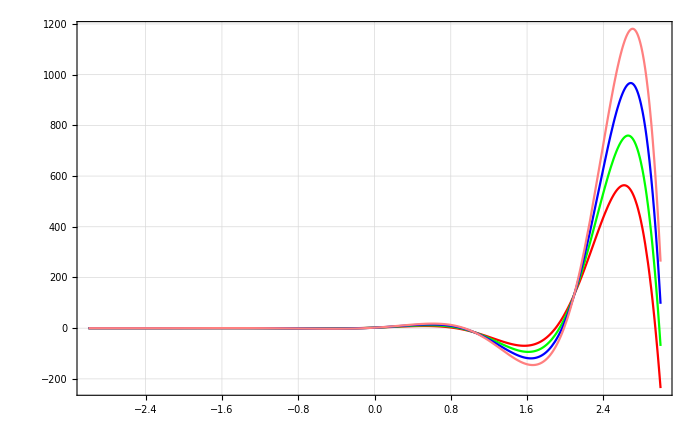

```mathematica
Plot[{c1},{x,-3,3},PlotStyle->{Red,Green,Blue,Pink},
Frame->True,AxesOrigin->{0,0},GridLines->Automatic,ImageSize->700,PlotRange->All]
```

Initial Value Problems

```mathematica
Ques 7: y''+y'-2y=0
```

```mathematica
p=DSolve[{y''[x]+y'[x]-2y[x]==0,y[0]==4,y'[0]==-5},y[x],x]
```

{{y[x]→ⅇ^(-2 x) (3+ⅇ^(3 x))}}

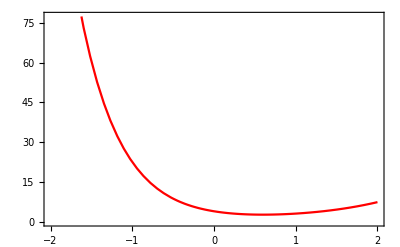

```mathematica
Plot[y[x]/.p,{x,-2,2},PlotStyle->{Red},Frame->True]
```

Non - Homogenous Differential Equation

```mathematica
Ques 8: y''-2y'-3y=30^(2x)
```

{{y[x]→-10 ⅇ^(2 x)+ⅇ^-x C[1]+ⅇ^(3 x) C[2]}}

{{3 ⅇ^-x-10 ⅇ^(2 x)+2 ⅇ^(3 x)},{4 ⅇ^-x-10 ⅇ^(2 x)+2 ⅇ^(3 x)},{5 ⅇ^-x-10 ⅇ^(2 x)+2 ⅇ^(3 x)},{6 ⅇ^-x-10 ⅇ^(2 x)+2 ⅇ^(3 x)}}

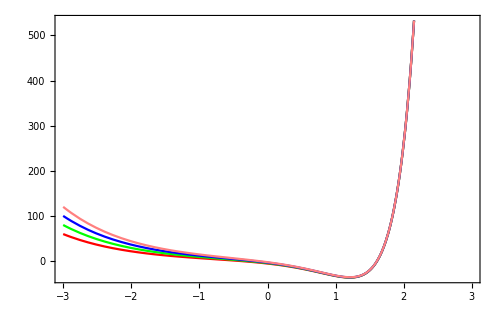

```mathematica
r=DSolve[y''[x]-2y'[x]-3y[x]==30Exp[2x],y[x],x]
a=Table[y[x]/.r/.{C[1]->k,C[2]->2},{k,3,6}]
Plot[{a},{x,-3,3},PlotStyle->{Red,Green,Blue,Pink},ImageSize->500,Frame->True,AxesOrigin->{0,0}]
```

```mathematica
Ques 9: y''-2y'-3y=2sinx
```

```mathematica
p=DSolve[y''[x]-2*y'[x]-3*y[x]==2*Sin[x],y[x],x]
p1=Table[y[x]/.p/.{C[1]->m,C[2]->m},{m,4,7}]
```

{{y[x]→ⅇ^-x C[1]+ⅇ^(3 x) C[2]+1/5 (Cos[x]-2 Sin[x])}}

{{4 ⅇ^-x+4 ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])},{5 ⅇ^-x+5 ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])},{6 ⅇ^-x+6 ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])},{7 ⅇ^-x+7 ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])}}

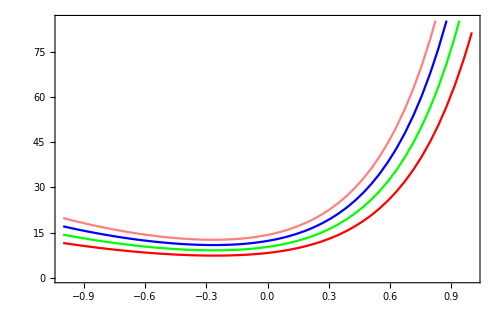

```mathematica
Plot[{p1},{x,-1,1},PlotStyle->{Red,Green,Blue,Pink},ImageSize->500,Frame->True,AxesOrigin->{0,0}]
```

```mathematica
{ (7 ⅇ^-x+7 ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x]))}}
```

```mathematica
p2=Table[y[x]/.p/.{C[1]->m,C[2]->m},{m,4,7}]
```

{{4 ⅇ^-x+4 ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])},{5 ⅇ^-x+5 ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])},{6 ⅇ^-x+6 ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])},{7 ⅇ^-x+7 ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])}}

```mathematica
Plot[{p2},{x,-1,1},PlotStyle->{Red,Green,Blue,Pink},ImageSize->500,Frame->True,AxesOrigin->{0,0}]
```

-Graphics-

{{4 ⅇ^-x+ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])},{5 ⅇ^-x+ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])},{6 ⅇ^-x+ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])},{7 ⅇ^-x+ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])}}

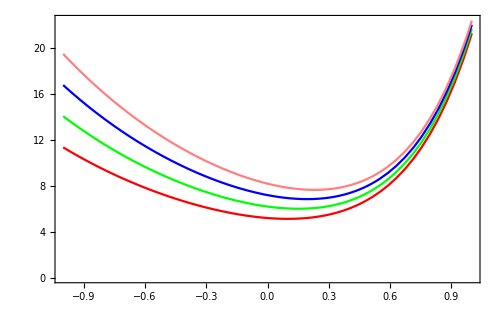

```mathematica
p3=Table[y[x]/.p/.{C[1]->m,C[2]->1},{m,4,7}]
Plot[{p3},{x,-1,1},PlotStyle->{Red,Green,Blue,Pink},ImageSize->500,Frame->True,AxesOrigin->{0,0}]
```

```mathematica
Initial Value Problems
```

```mathematica
Ques 10: y''+y=0.001x^2
```

{{y[x]→-0.002+0.001 x^2+0.002 Cos[1. x]+1.5 Sin[1. x]}}

{-0.002+0.001 x^2+0.002 Cos[1. x]+1.5 Sin[1. x]}

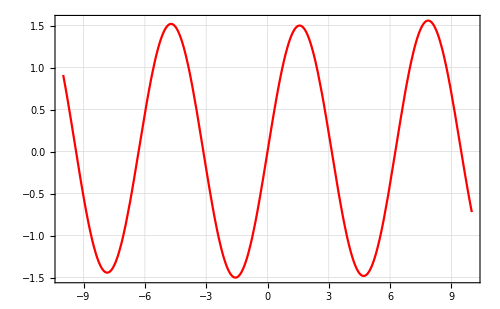

```mathematica
q2=DSolve[{y''[x]+y[x]==.001x^2,y[0]==0,y'[0]==1.5},y[x],x]
q3=Table[y[x]/.q2]
Plot[{q3},{x,-10,10},PlotStyle->{Red},GridLines->Automatic,PlotLegends->Automatic,Frame->True,AxesOrigin->{0,0}]
```

```mathematica
Euler and Cauchy equation
```

```mathematica
Ques 11: x^2 y''-2xy'-4y=0.001x^2
```

{{y[x]→x^(1/2 (1-√17)) C[1]+x^(1/2 (1+√17)) C[2]+x^(1/2-(√17)/2) (-(2 K[1]^(-3/2+(√17)/2) xy'[K[1]])/(√17)K[1]1x+x^(√17) (2 K[2]^(-3/2-(√17)/2) xy'[K[2]])/(√17)K[2]1x)}}

{{-0.002+0.001 x^2+0.002 Cos[1. x]+1.5 Sin[1. x]},{-0.002+0.001 x^2+0.002 Cos[1. x]+1.5 Sin[1. x]},{-0.002+0.001 x^2+0.002 Cos[1. x]+1.5 Sin[1. x]},{-0.002+0.001 x^2+0.002 Cos[1. x]+1.5 Sin[1. x]}}

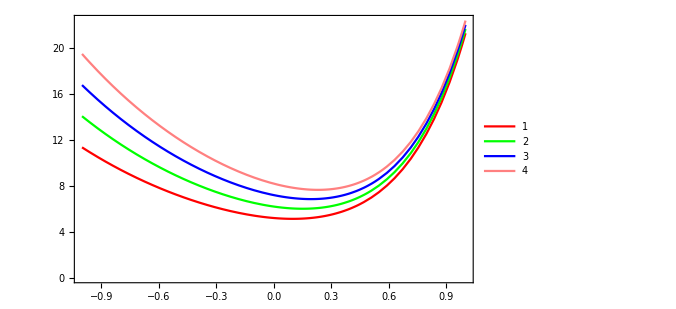

```mathematica
b=DSolve[x^2y''[x]-2xy'[x]-4y[x]==0,y[x],x]
c=Table[y[x]/.q2/.{C[1]->k,C[2]->2},{k,3,6}]
Plot[{p3},{x,-1,1},PlotStyle->{Red,Green,Blue,Pink},ImageSize->500,Frame->True,AxesOrigin->{0,0},PlotLegends->Automatic]
```

# PRACTICAL 3: PLOTTING THIRD ORDER SOLUTION FAMILY OF DIFFERENTIAL EQUATION

### Ques 1 : y'' + y = 0.001 x^2

```mathematica
Sol = DSolve[y'''[x]-5y''y[x]+8y'[x]-4y[x]==0,y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^(2 x) C[2]+ⅇ^(2 x) x C[3]}}

```mathematica
Sol1=Evaluate[y[x]/.Sol[[1]]/.{C[1]->1,C[2]->2,C[3]->2/3}]
```

ⅇ^x+2 ⅇ^(2 x)+2/3 ⅇ^(2 x) x

```mathematica
Sol2=Evaluate[y[x]/.Sol[[1]]/.{C[1]->0.5,C[2]->2,C[3]->3}]
```

0.5 ⅇ^x+2 ⅇ^(2 x)+3 ⅇ^(2 x) x

```mathematica
Sol3=Evaluate[y[x]/.Sol[[1]]/.{C[1]->-1,C[2]->-2,C[3]->0.5}]
```

-ⅇ^-x-2 ⅇ^(3 x)+0.5 ⅇ^(11 x)+(17 Cos[2 x]+6 Sin[2 x])/1625

```mathematica
Plot[{Sol1,Sol2,Sol3},{x,-1,1},ImageSize->700,PlotStyle->{{Red,Thickness[0.02]},{Green,Thick},{Blue,Thickness[0.01]}},
PlotLegends->Placed[LineLegend["Expressions",LegendLayout->"Column",LegendFunction->"Frame"],{0.15,0.87}]]
```

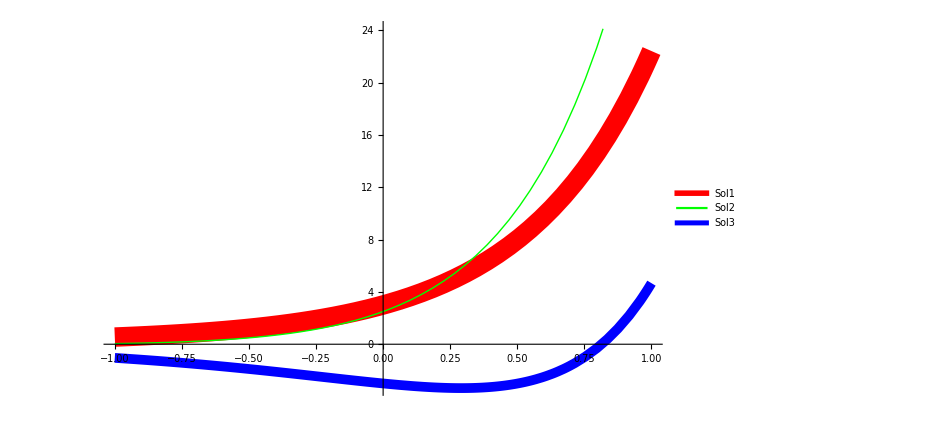

### Ques 2: y’’’+3y’’-25y’+21y=0

```mathematica
sol=DSolve[y'''[x]+3y''[x]-25y'[x]+21y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(-7 x) C[1]+ⅇ^x C[2]+ⅇ^(3 x) C[3]}}

```mathematica
sol1=Evaluate[y[x]/.sol[[1]]/.{C[1]->1,C[2]->2,C[3]->3}]
```

ⅇ^(-7 x)+2 ⅇ^x+3 ⅇ^(3 x)

```mathematica
sol2=Evaluate[y[x]/.sol[[1]]/.{C[1]->0.5,C[2]->2,C[3]->-1}]
```

0.5 ⅇ^(-7 x)+2 ⅇ^x-ⅇ^(3 x)

```mathematica
sol3=Evaluate[y[x]/.sol[[1]]/.{C[1]->-1,C[2]->-2,C[3]->0.5}]
```

-ⅇ^(-7 x)-2 ⅇ^x+0.5 ⅇ^(3 x)

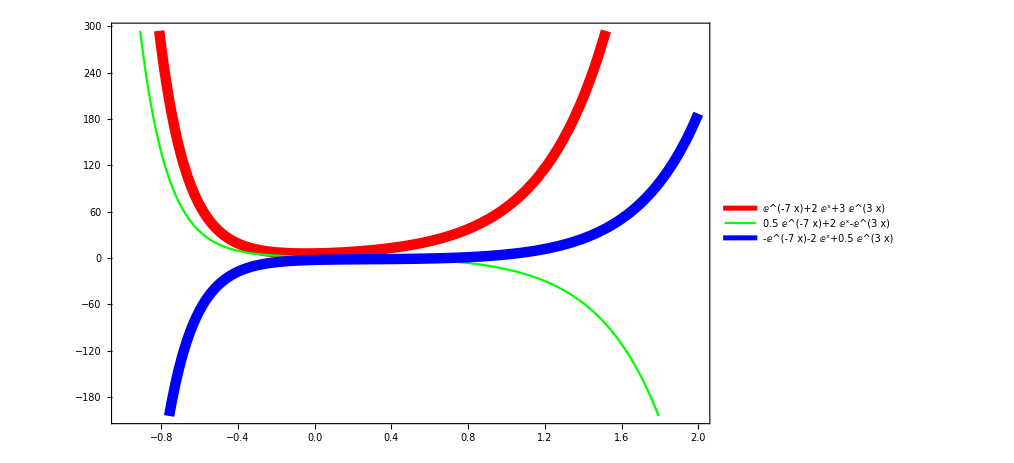

```mathematica
Plot[{sol1,sol2,sol3},{x,-1,2},PlotStyle->{{Red,Thickness[0.01]},{Green,Thick},{Blue,Thickness[0.01]}},
PlotLegends->{sol1,sol2,sol3},Frame->True,ImageSize->750]
```

### Ques 3 : y’’’-4y’’-25y’+28y=0

```mathematica
pol=DSolve[y'''[x]-4y''[x]-25y'[x]+28y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(-4 x) C[1]+ⅇ^x C[2]+ⅇ^(7 x) C[3]}}

```mathematica
pol1= Evaluate[y[x]/.pol[[1]]/.{C[1]->1,C[2]->2,C[3]->3}]
```

ⅇ^(-4 x)+2 ⅇ^x+3 ⅇ^(7 x)

```mathematica
pol2= Evaluate[y[x]/.pol[[1]]/.{C[1]->-1,C[2]->-2,C[3]->1.3}]
```

-ⅇ^(-4 x)-2 ⅇ^x+1.3 ⅇ^(7 x)

```mathematica
pol3= Evaluate[y[x]/.pol[[1]]/.{C[1]->3/2,C[2]->0.5,C[3]->-2.5}]
```

(3 ⅇ^(-4 x))/2+0.5 ⅇ^x-2.5 ⅇ^(7 x)

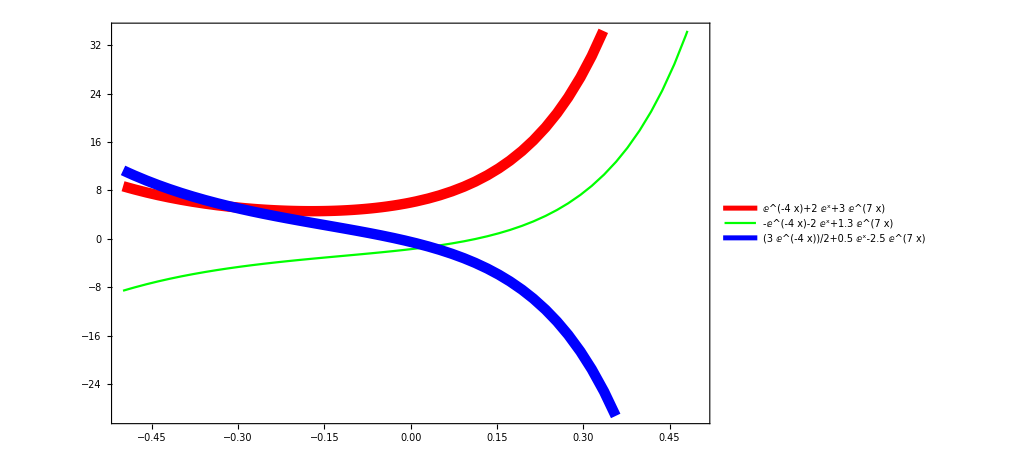

```mathematica
Plot[{pol1,pol2,pol3},{x,-0.5,0.5},PlotStyle->{{Red,Thickness[0.01]},{Green,Thick},{Blue,Thickness[0.01]}},
PlotLegends->{pol1,pol2,pol3},Frame->True,ImageSize->750]
```

### Ques 4 : y’’’-13y’’+19y’+33y=Cos2x

{{y[x]→ⅇ^-x C[1]+ⅇ^(3 x) C[2]+ⅇ^(11 x) C[3]+(17 Cos[2 x]+6 Sin[2 x])/1625}}

ⅇ^-x+2 ⅇ^(3 x)+3 ⅇ^(11 x)+(17 Cos[2 x]+6 Sin[2 x])/1625

-ⅇ^-x-2 ⅇ^(3 x)+1.3 ⅇ^(11 x)+(17 Cos[2 x]+6 Sin[2 x])/1625

(3 ⅇ^-x)/2+0.5 ⅇ^(3 x)-2.5 ⅇ^(11 x)+(17 Cos[2 x]+6 Sin[2 x])/1625

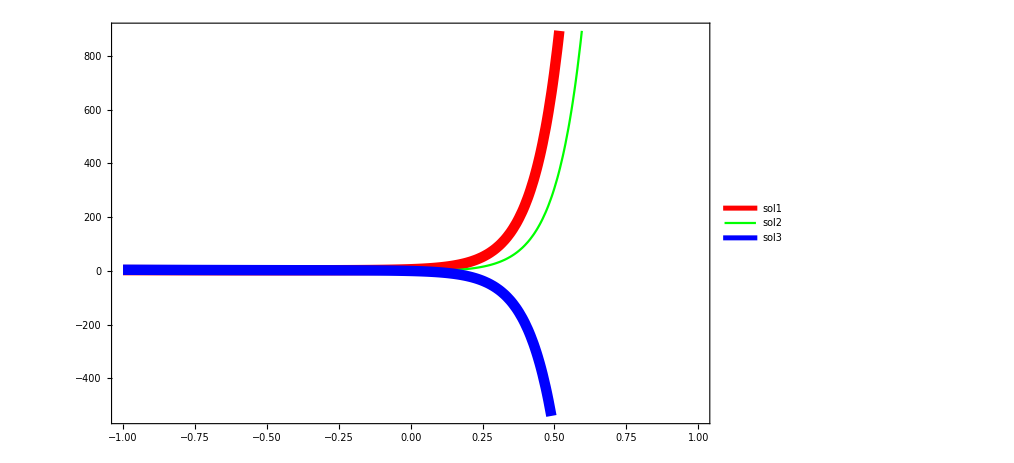

```mathematica
Sol=DSolve[y'''[x]-13y''[x]+19y'[x]+33y[x]==Cos[2x],y[x],x]
sol1= Evaluate[y[x]/.Sol[[1]]/.{C[1]->1,C[2]->2,C[3]->3}]
sol2= Evaluate[y[x]/.Sol[[1]]/.{C[1]->-1,C[2]->-2,C[3]->1.3}]
sol3= Evaluate[y[x]/.Sol[[1]]/.{C[1]->3/2,C[2]->0.5,C[3]->-2.5}]
Plot[{sol1,sol2,sol3},{x,-1,1},PlotStyle->{{Red,Thickness[0.01]},{Green,Thick},{Blue,Thickness[0.01]}},
Frame->True,ImageSize->750,PlotLegends->Placed[{"sol1","sol2","sol3"},Below]]
```

### Ques 5 : y’’’ - 6y’’ + 5y’ + 12y = 0

{{y[x]→ⅇ^-x C[1]+ⅇ^(3 x) C[2]+ⅇ^(4 x) C[3]}}

ⅇ^-x+2 ⅇ^(3 x)+3 ⅇ^(4 x)

-ⅇ^-x-2 ⅇ^(3 x)+1.3 ⅇ^(4 x)

(3 ⅇ^-x)/2+0.5 ⅇ^(3 x)-2.5 ⅇ^(4 x)

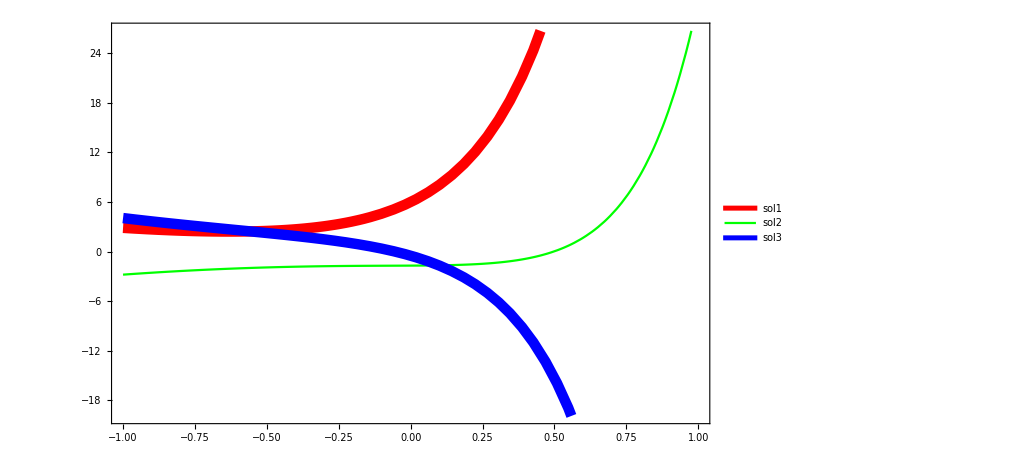

```mathematica
Sol=DSolve[y'''[x]-6y''[x]+5y'[x]+12y[x]==0,y[x],x]
sol1= Evaluate[y[x]/.Sol[[1]]/.{C[1]->1,C[2]->2,C[3]->3}]
sol2= Evaluate[y[x]/.Sol[[1]]/.{C[1]->-1,C[2]->-2,C[3]->1.3}]
sol3= Evaluate[y[x]/.Sol[[1]]/.{C[1]->3/2,C[2]->0.5,C[3]->-2.5}]
Plot[{sol1,sol2,sol3},{x,-1,1},PlotStyle->{{Red,Thickness[0.01]},{Green,Thick},{Blue,Thickness[0.01]}},
Frame->True,ImageSize->750,PlotLegends->Placed[{"sol1","sol2","sol3"},Below]]
```

### Ques 6 : y’’’ - 6y’’ + 11y’ - 6y = 0

{{y[x]→ⅇ^x C[1]+ⅇ^(2 x) C[2]+ⅇ^(3 x) C[3]}}

ⅇ^x+2 ⅇ^(2 x)+3 ⅇ^(3 x)

-ⅇ^x-2 ⅇ^(2 x)+1.3 ⅇ^(3 x)

(3 ⅇ^x)/2+0.5 ⅇ^(2 x)-2.5 ⅇ^(3 x)

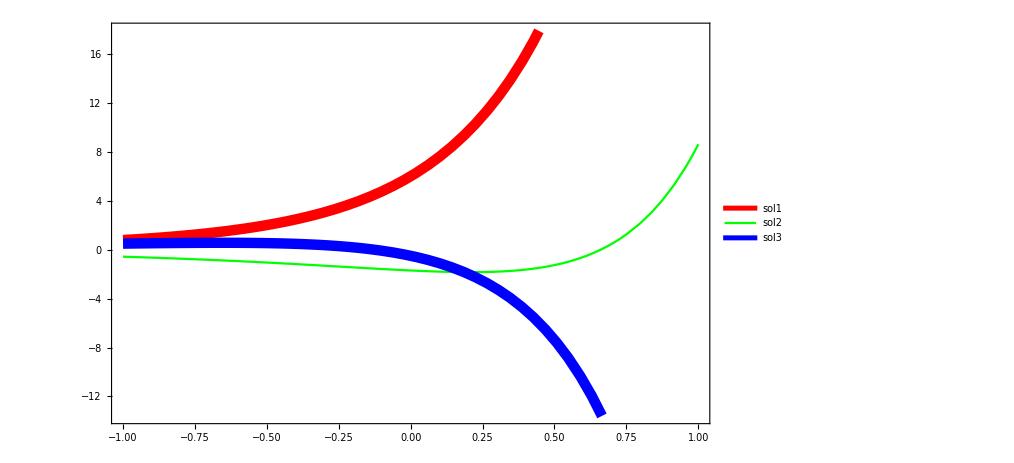

```mathematica
Sol=DSolve[y'''[x]-6y''[x]+11y'[x]-6y[x]==0,y[x],x]
sol1= Evaluate[y[x]/.Sol[[1]]/.{C[1]->1,C[2]->2,C[3]->3}]
sol2= Evaluate[y[x]/.Sol[[1]]/.{C[1]->-1,C[2]->-2,C[3]->1.3}]
sol3= Evaluate[y[x]/.Sol[[1]]/.{C[1]->3/2,C[2]->0.5,C[3]->-2.5}]
Plot[{sol1,sol2,sol3},{x,-1,1},PlotStyle->{{Red,Thickness[0.01]},{Green,Thick},{Blue,Thickness[0.01]}},
Frame->True,ImageSize->750,PlotLegends->Placed[{"sol1","sol2","sol3"},Below]]
```

### Ques 7 : y’’’ + y’ = sec x

{{y[x]→C[3]-x Cos[x]-C[2] Cos[x]-Log[Cos[x/2]-Sin[x/2]]+Log[Cos[x/2]+Sin[x/2]]+C[1] Sin[x]+Log[Cos[x]] Sin[x]}}

3-2 Cos[x]-x Cos[x]-Log[Cos[x/2]-Sin[x/2]]+Log[Cos[x/2]+Sin[x/2]]+Sin[x]+Log[Cos[x]] Sin[x]

1.3+2 Cos[x]-x Cos[x]-Log[Cos[x/2]-Sin[x/2]]+Log[Cos[x/2]+Sin[x/2]]-Sin[x]+Log[Cos[x]] Sin[x]

-2.5-0.5 Cos[x]-x Cos[x]-Log[Cos[x/2]-Sin[x/2]]+Log[Cos[x/2]+Sin[x/2]]+(3 Sin[x])/2+Log[Cos[x]] Sin[x]

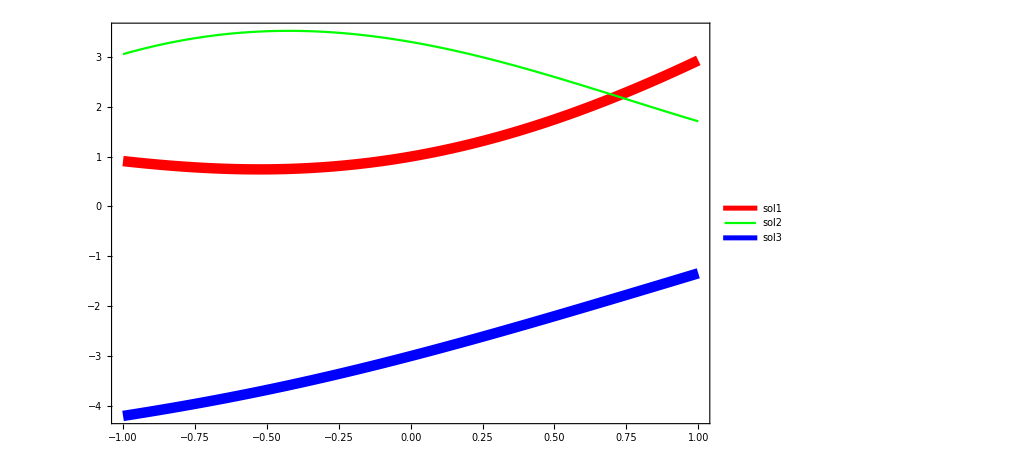

```mathematica
Sol=DSolve[y'''[x]+y'[x]==Sec[x],y[x],x]
sol1= Evaluate[y[x]/.Sol[[1]]/.{C[1]->1,C[2]->2,C[3]->3}]
sol2= Evaluate[y[x]/.Sol[[1]]/.{C[1]->-1,C[2]->-2,C[3]->1.3}]
sol3= Evaluate[y[x]/.Sol[[1]]/.{C[1]->3/2,C[2]->0.5,C[3]->-2.5}]
Plot[{sol1,sol2,sol3},{x,-1,1},PlotStyle->{{Red,Thickness[0.01]},{Green,Thick},{Blue,Thickness[0.01]}},
Frame->True,ImageSize->750,PlotLegends->Placed[{"sol1","sol2","sol3"},Below]]
```

# PRACTICAL 5 : SOLUTION OF SYSTEM OF ORDINARY DIFFERENTIAL EQUATION

### Ques 1 : Solve the following system of equations : x' = -3 x - y y' = -x - 3 y

```mathematica
eq1={x'[t]==-3*x[t]-y[t],y'[t]==-3y[t]-x[t]}
```

{x'[t]==-3 x[t]-y[t],y'[t]==-x[t]-3 y[t]}

```mathematica
sol=DSolve[eq1,{y[t],x[t]},t]
```

{{x[t]→1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)) C[1]-1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t)) C[2],y[t]→-1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t)) C[1]+1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)) C[2]}}

```mathematica
tabx=Table[x[t]/.sol[[1,1]]/.{C[1]->i,C[2]->j},{i,-1,0},{j,0,1}]//Flatten
```

{-1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)),-1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t))-1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)),0,-1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t))}

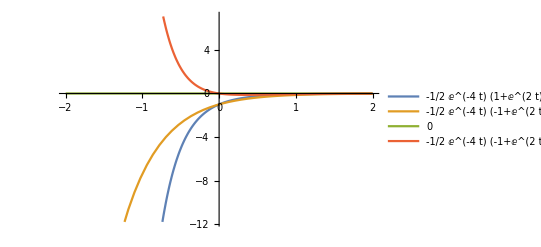

```mathematica
Plot[Evaluate[tabx],{t,-2,2},PlotLegends->"Expressions"]
```

```mathematica
taby=Table[y[t]/.sol[[1,2]]/.{C[1]->i,C[2]->j},{i,-1,0},{j,0,1}]//Flatten
```

{1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t)),1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t))+1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)),0,1/2 ⅇ^(-4 t) (1+ⅇ^(2 t))}

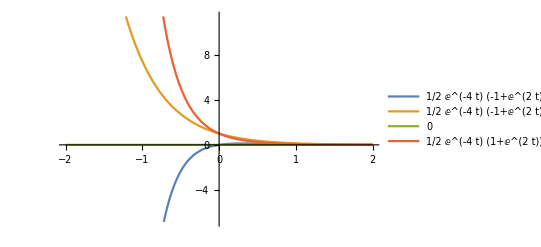

```mathematica
Plot[Evaluate[taby],{t,-2,2},PlotLegends->"Expressions"]
```

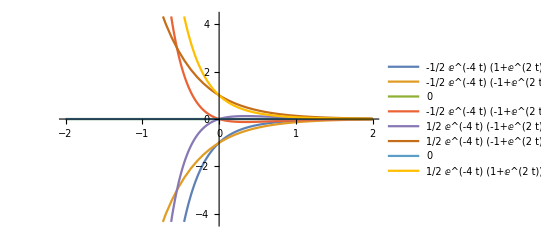

```mathematica
Plot[Evaluate[{tabx,taby}],{t,-2,2},PlotLegends->"Expressions"]
```

### Ques 2 : Solve the following system of equations : x' = y y' = 6 x - y with inital conditions x (0) = 1 , y (0) = -2

```mathematica
eq2={{x'[t]== y[t],y'[t]==-y[t]+6x[t]},x[0]==1,y[0]==-2}
```

{{x'[t]==y[t],y'[t]==6 x[t]-y[t]},x[0]==1,y[0]==-2}

```mathematica
DSolve[eq1,{x[t],y[t]},t]
```

{{x[t]→1/5 ⅇ^(-3 t) (4+ⅇ^(5 t)),y[t]→2/5 ⅇ^(-3 t) (-6+ⅇ^(5 t))}}

```mathematica
{xsol[t_],ysol[t_]}=ExpandAll[{x[t],y[t]}/.Flatten[DSolve[eq2,{x[t],y[t]},t]]]
```

{(4 ⅇ^(-3 t))/5+ⅇ^(2 t)/5,-12/5 ⅇ^(-3 t)+(2 ⅇ^(2 t))/5}

```mathematica
xsol[t]
```

(4 ⅇ^(-3 t))/5+ⅇ^(2 t)/5

```mathematica
ysol[t]
```

-12/5 ⅇ^(-3 t)+(2 ⅇ^(2 t))/5

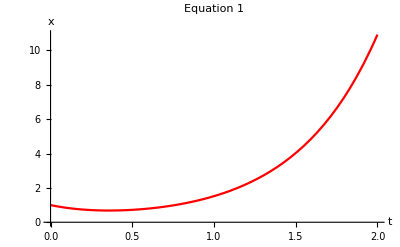

```mathematica
plot1= Plot[xsol[t],{t,0,2},AxesLabel->{"t","x"},PlotLabel->"Equation 1",PlotStyle ->{Red}]
```

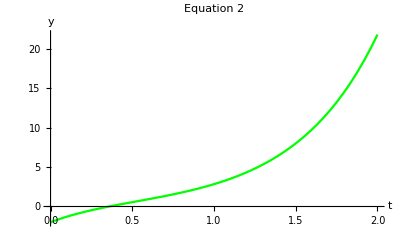

```mathematica
plot1= Plot[ysol[t],{t,0,2},AxesLabel->{"t","y"},PlotLabel->"Equation 2",PlotStyle ->{Green}]
```

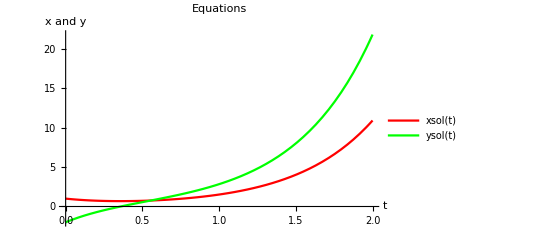

```mathematica
Plot[{xsol[t],ysol[t]},{t,0,2},AxesLabel->{"t","x and y"},PlotLabel->"Equations",PlotLegends->"Expressions",PlotStyle ->{Red,Green}]
```

### Ques 3 : Solve the following system of equations : x' = 5 x - 2 y y' = 4 x - y

```mathematica
eq1={x'[t]==5*x[t]-2y[t],y'[t]==4x[t]-y[t]}
```

{x'[t]==5 x[t]-2 y[t],y'[t]==4 x[t]-y[t]}

```mathematica
sol=DSolve[eq1,{y[t],x[t]},t]
```

{{x[t]→ⅇ^t (-1+2 ⅇ^(2 t)) C[1]-ⅇ^t (-1+ⅇ^(2 t)) C[2],y[t]→2 ⅇ^t (-1+ⅇ^(2 t)) C[1]-ⅇ^t (-2+ⅇ^(2 t)) C[2]}}

```mathematica
tabx=Table[x[t]/.sol[[1,1]]/.{C[1]->i,C[2]->j},{i,-2,0},{j,0,2}]//Flatten
```

{-2 ⅇ^t (-1+2 ⅇ^(2 t)),-ⅇ^t (-1+ⅇ^(2 t))-2 ⅇ^t (-1+2 ⅇ^(2 t)),-2 ⅇ^t (-1+ⅇ^(2 t))-2 ⅇ^t (-1+2 ⅇ^(2 t)),-ⅇ^t (-1+2 ⅇ^(2 t)),-ⅇ^t (-1+ⅇ^(2 t))-ⅇ^t (-1+2 ⅇ^(2 t)),-2 ⅇ^t (-1+ⅇ^(2 t))-ⅇ^t (-1+2 ⅇ^(2 t)),0,-ⅇ^t (-1+ⅇ^(2 t)),-2 ⅇ^t (-1+ⅇ^(2 t))}

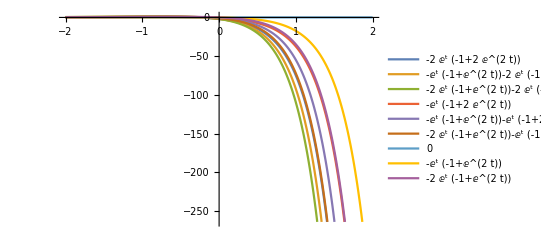

```mathematica
Plot[Evaluate[tabx],{t,-2,2},PlotLegends->"Expressions"]
```

```mathematica
taby=Table[y[t]/.sol[[1,2]]/.{C[1]->i,C[2]->j},{i,-2,0},{j,0,2}]//Flatten
```

{-4 ⅇ^t (-1+ⅇ^(2 t)),-ⅇ^t (-2+ⅇ^(2 t))-4 ⅇ^t (-1+ⅇ^(2 t)),-2 ⅇ^t (-2+ⅇ^(2 t))-4 ⅇ^t (-1+ⅇ^(2 t)),-2 ⅇ^t (-1+ⅇ^(2 t)),-ⅇ^t (-2+ⅇ^(2 t))-2 ⅇ^t (-1+ⅇ^(2 t)),-2 ⅇ^t (-2+ⅇ^(2 t))-2 ⅇ^t (-1+ⅇ^(2 t)),0,-ⅇ^t (-2+ⅇ^(2 t)),-2 ⅇ^t (-2+ⅇ^(2 t))}

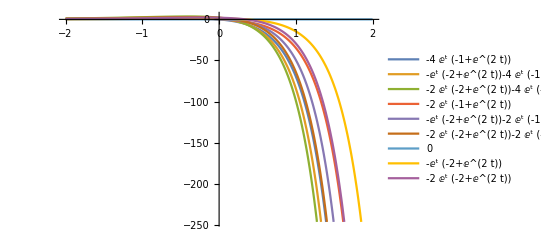

```mathematica
Plot[Evaluate[taby],{t,-2,2},PlotLegends->"Expressions"]
```

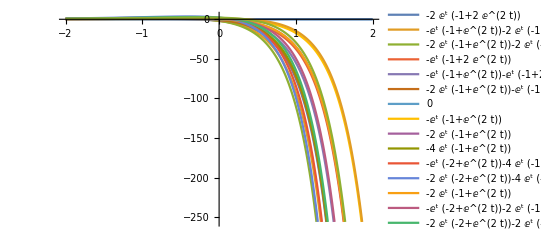

```mathematica
Plot[Evaluate[{tabx,taby}],{t,-2,2},PlotLegends->"Expressions"]
```

### Ques 4 : Solve the following system of equations : x' = 3 x - 4 y y' = 2 x - y

```mathematica
eq1={x'[t]==3*x[t]-4y[t],y'[t]==2x[t]-y[t]}
```

{x'[t]==3 x[t]-4 y[t],y'[t]==2 x[t]-y[t]}

```mathematica
sol=DSolve[eq1,{y[t],x[t]},t]
```

{{x[t]→-2 ⅇ^t C[2] Sin[2 t]+ⅇ^t C[1] (Cos[2 t]+Sin[2 t]),y[t]→ⅇ^t C[2] (Cos[2 t]-Sin[2 t])+ⅇ^t C[1] Sin[2 t]}}

```mathematica
tabx=Table[x[t]/.sol[[1,1]]/.{C[1]->i,C[2]->j},{i,-2,0},{j,0,2}]//Flatten
```

{-2 ⅇ^t (Cos[2 t]+Sin[2 t]),-2 ⅇ^t Sin[2 t]-2 ⅇ^t (Cos[2 t]+Sin[2 t]),-4 ⅇ^t Sin[2 t]-2 ⅇ^t (Cos[2 t]+Sin[2 t]),-ⅇ^t (Cos[2 t]+Sin[2 t]),-2 ⅇ^t Sin[2 t]-ⅇ^t (Cos[2 t]+Sin[2 t]),-4 ⅇ^t Sin[2 t]-ⅇ^t (Cos[2 t]+Sin[2 t]),0,-2 ⅇ^t Sin[2 t],-4 ⅇ^t Sin[2 t]}

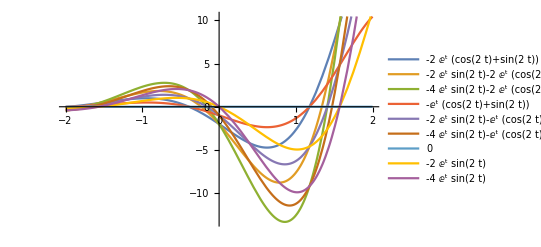

```mathematica
Plot[Evaluate[tabx],{t,-2,2},PlotLegends->"Expressions"]
```

```mathematica
taby=Table[y[t]/.sol[[1,2]]/.{C[1]->i,C[2]->j},{i,-2,0},{j,0,2}]//Flatten
```

{-2 ⅇ^t Sin[2 t],ⅇ^t (Cos[2 t]-Sin[2 t])-2 ⅇ^t Sin[2 t],2 ⅇ^t (Cos[2 t]-Sin[2 t])-2 ⅇ^t Sin[2 t],-ⅇ^t Sin[2 t],ⅇ^t (Cos[2 t]-Sin[2 t])-ⅇ^t Sin[2 t],2 ⅇ^t (Cos[2 t]-Sin[2 t])-ⅇ^t Sin[2 t],0,ⅇ^t (Cos[2 t]-Sin[2 t]),2 ⅇ^t (Cos[2 t]-Sin[2 t])}

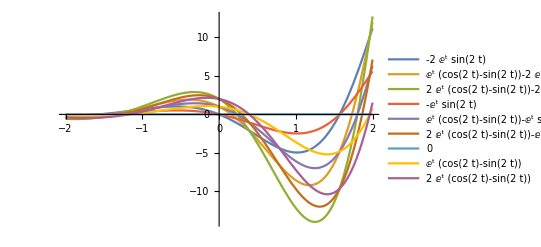

```mathematica
Plot[Evaluate[taby],{t,-2,2},PlotLegends->"Expressions"]
```

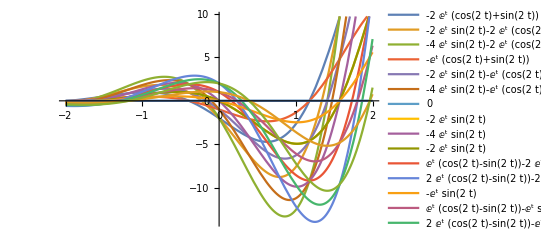

```mathematica
Plot[Evaluate[{tabx,taby}],{t,-2,2},PlotLegends->"Expressions"]
```

### Ques 5 : Solve the following system of equations : x' = 2 x + 7 y y' = 3 x + 2 y with inital conditions x (0) = 9, y (0) = -1

```mathematica
eq2={{x'[t]== 2x[t]+7y[t],y'[t]==3x[t]+2y[t]},x[0]==9,y[0]==-1}
```

{{x'[t]==2 x[t]+7 y[t],y'[t]==3 x[t]+2 y[t]},x[0]==9,y[0]==-1}

```mathematica
DSolve[eq1,{x[t],y[t]},t]
```

{{x[t]→-2 ⅇ^t C[2] Sin[2 t]+ⅇ^t C[1] (Cos[2 t]+Sin[2 t]),y[t]→ⅇ^t C[2] (Cos[2 t]-Sin[2 t])+ⅇ^t C[1] Sin[2 t]}}

```mathematica
{xsol[t_],ysol[t_]}=ExpandAll[{x[t],y[t]}/.Flatten[DSolve[eq2,{x[t],y[t]},t]]]
```

{9/2 ⅇ^(2 t-√21 t)+1/2 √(7/3) ⅇ^(2 t-√21 t)+9/2 ⅇ^(2 t+√21 t)-1/2 √(7/3) ⅇ^(2 t+√21 t),-1/2 ⅇ^(2 t-√21 t)-9/2 √(3/7) ⅇ^(2 t-√21 t)-1/2 ⅇ^(2 t+√21 t)+9/2 √(3/7) ⅇ^(2 t+√21 t)}

```mathematica
xsol[t]
```

9/2 ⅇ^(2 t-√21 t)+1/2 √(7/3) ⅇ^(2 t-√21 t)+9/2 ⅇ^(2 t+√21 t)-1/2 √(7/3) ⅇ^(2 t+√21 t)

```mathematica
ysol[t]
```

-1/2 ⅇ^(2 t-√21 t)-9/2 √(3/7) ⅇ^(2 t-√21 t)-1/2 ⅇ^(2 t+√21 t)+9/2 √(3/7) ⅇ^(2 t+√21 t)

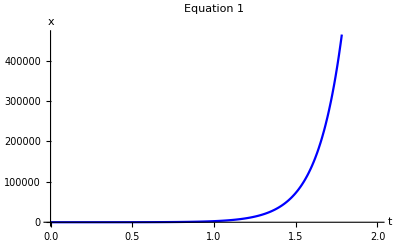

```mathematica
plot1= Plot[xsol[t],{t,0,2},AxesLabel->{"t","x"},PlotLabel->"Equation 1",PlotStyle ->{Blue}]
```

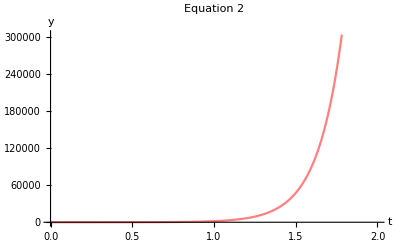

```mathematica
plot1= Plot[ysol[t],{t,0,2},AxesLabel->{"t","y"},PlotLabel->"Equation 2",PlotStyle ->{Pink}]
```

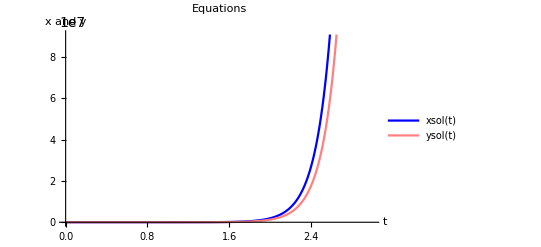

```mathematica
Plot[{xsol[t],ysol[t]},{t,0,3},AxesLabel->{"t","x and y"},PlotLabel->"Equations",PlotLegends->"Expressions",PlotStyle ->{Blue,Pink}]
```

### Ques 6 : Solve the following system of equations : x' = 7 x - y y' = 4 x + 3 y with inital conditions x (0) = 1, y (0) = 3

```mathematica
eq2={{x'[t]== 7x[t]-y[t],y'[t]==4x[t]+3y[t]},x[0]==1,y[0]==3}
```

{{x'[t]==7 x[t]-y[t],y'[t]==4 x[t]+3 y[t]},x[0]==1,y[0]==3}

```mathematica
DSolve[eq1,{x[t],y[t]},t]
```

{{x[t]→-2 ⅇ^t C[2] Sin[2 t]+ⅇ^t C[1] (Cos[2 t]+Sin[2 t]),y[t]→ⅇ^t C[2] (Cos[2 t]-Sin[2 t])+ⅇ^t C[1] Sin[2 t]}}

```mathematica
{xsol[t_],ysol[t_]}=ExpandAll[{x[t],y[t]}/.Flatten[DSolve[eq2,{x[t],y[t]},t]]]
```

{ⅇ^(5 t)-ⅇ^(5 t) t,3 ⅇ^(5 t)-2 ⅇ^(5 t) t}

```mathematica
xsol[t]
```

ⅇ^(5 t)-ⅇ^(5 t) t

```mathematica
ysol[t]
```

3 ⅇ^(5 t)-2 ⅇ^(5 t) t

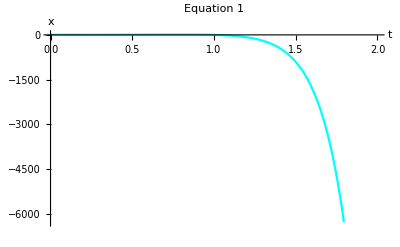

```mathematica
plot1= Plot[xsol[t],{t,0,2},AxesLabel->{"t","x"},PlotLabel->"Equation 1",PlotStyle ->{Cyan}]
```

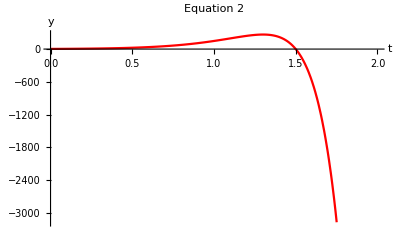

```mathematica
plot1= Plot[ysol[t],{t,0,2},AxesLabel->{"t","y"},PlotLabel->"Equation 2",PlotStyle ->{Red}]
```

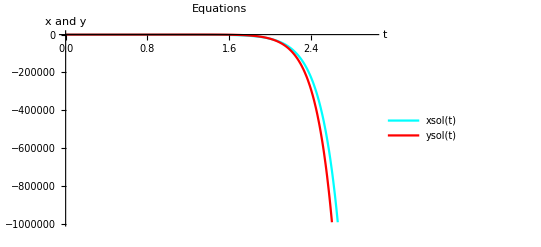

```mathematica
Plot[{xsol[t],ysol[t]},{t,0,3},AxesLabel->{"t","x and y"},PlotLabel->"Equations",PlotLegends->"Expressions",PlotStyle ->{Cyan,Red}]
```

# PRACTICAL 6 : SOLUTION OF CAUCHY PROBLEM FOR FIRST ORDER PARTIAL DIFFERENTIAL EQUATION

### Ques 1 :u_x-u_y=1,u(x,0)=x^2

```mathematica
sol=DSolve[{D[u[x,y],x]-D[u[x,y],y]==1,u[x,0]==x^2},u[x,y],{x,y}]
```

{{u[x,y]→x^2-y+2 x y+y^2}}

```mathematica
Plot3D[u[x,y]/.sol,{x,-4,4},{y,-4,4}]
```

-Graphics3D-

### Ques 2 :u_x+u_y=u,u(x,0)=x^3

```mathematica
sol2=DSolve[{D[u[x,y],x]+D[u[x,y],y]==u[x,y],u[x,0]==x^3},u[x,y],{x,y}]
```

{{u[x,y]→-ⅇ^y (-x+y)^3}}

```mathematica
Plot3D[u[x,y]/.sol2,{x,0,2},{y,0,1}]
```

-Graphics3D-

### Ques 3 : yu_x+xu_y=u,u(0,y)=y^3

```mathematica
sol3=DSolve[{y D[u[x,y],x]+x D[u[x,y],y]==u[x,y],u[0,y]==y^3},u[x,y],{x,y}]
```

{{u[x,y]→-((-x^2+y^2)^(3/2) √(1-x/(√(y^2))))/(√(1+x/(√(y^2))))},{u[x,y]→-((-x^2+y^2)^(3/2) √(1+x/(√(y^2))))/(√(1-x/(√(y^2))))}}

```mathematica
sol3[[1,1]]
```

u[x,y]→-((-x^2+y^2)^(3/2) √(1-x/(√(y^2))))/(√(1+x/(√(y^2))))

```mathematica
sol3[[2,1]]
```

u[x,y]→-((-x^2+y^2)^(3/2) √(1+x/(√(y^2))))/(√(1-x/(√(y^2))))

```mathematica
Plot3D[u[x,y]/.sol3[[1,1]],{x,1,3},{y,1,2}]
```

-Graphics3D-

```mathematica
Plot3D[u[x,y]/.sol3[[2,1]],{x,1,3},{y,1,2}]
```

-Graphics3D-

### Ques 4 : u_x+xu_y=0,u(0,y)=sin y

```mathematica
sol=DSolve[{ D[u[x,y],x]+x D[u[x,y],y]==0,u[0,y]==Sin[y]},u[x,y],{x,y}]
```

{{u[x,y]→Sin[1/2 (-x^2+2 y)]}}

```mathematica
Plot3D[u[x,y]/.sol,{x,-2,2},{y,-2,2},ColorFunction-> "Rainbow"]
```

-Graphics3D-

### Ques 5 : u(x+y)u_x+u(x-y)u_y=x^2+y^2,u=0,y=2x

```mathematica
sol=DSolve[{ u[x,y]*(x+y)*D[u[x,y],x]+u[x,y]*(x-y)*D[u[x,y],y]==x^2+y^2, u[x,2 x]==0},u[x,y],{x,y}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{u[x,y]→-√(2/7) √(2 x^2+3 x y-2 y^2)},{u[x,y]→√(2/7) √(2 x^2+3 x y-2 y^2)},{u[x,y]→-√(2/7) √(2 x^2+3 x y-2 y^2)},{u[x,y]→√(2/7) √(2 x^2+3 x y-2 y^2)}}

```mathematica
sol[[1,1]]
```

u[x,y]→-√(2/7) √(2 x^2+3 x y-2 y^2)

```mathematica
Plot3D[u[x,y]/.sol[[1,1]],{x,1,2},{y,1,3},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
sol[[2,1]]
```

u[x,y]→√(2/7) √(2 x^2+3 x y-2 y^2)

```mathematica
Plot3D[u[x,y]/.sol[[2,1]],{x,1,2},{y,1,3},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
sol[[3,1]]
```

u[x,y]→-√(2/7) √(2 x^2+3 x y-2 y^2)

```mathematica
Plot3D[u[x,y]/.sol[[3,1]],{x,1,2},{y,1,3},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
sol[[4,1]]
```

u[x,y]→√(2/7) √(2 x^2+3 x y-2 y^2)

```mathematica
Plot3D[u[x,y]/.sol[[4,1]],{x,1,2},{y,1,3},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

### Ques 6 : u_x+xu_y=(y-1/2 x^2)^2,u(0,y)=e^y

```mathematica
sol6=DSolve[{D[u[x,y],x]+x D[u[x,y],y]==(y-1/2 x^2)^2,u[0,y]==Exp[y]},u[x,y],{x,y}]
```

{{u[x,y]→1/4 ⅇ^(-x^2/2) (4 ⅇ^y+ⅇ^(x^2/2) x^5-4 ⅇ^(x^2/2) x^3 y+4 ⅇ^(x^2/2) x y^2)}}

```mathematica
sol6[[1,1]]
```

u[x,y]→1/4 ⅇ^(-x^2/2) (4 ⅇ^y+ⅇ^(x^2/2) x^5-4 ⅇ^(x^2/2) x^3 y+4 ⅇ^(x^2/2) x y^2)

```mathematica
Plot3D[u[x,y]/.sol6,{x,2,4},{y,1,3},ColorFunction->"Rainbow"]
```

-Graphics3D-

# PRACTICAL 7: PLOTTING THE CHARACTERISTIC FOR FIRST ORDER PARTIAL DIFFERENTIAL EQUATION

### Ques 1 :yu_x+xu_y=0

The characteristic system is given by dx/y=dy/x=du/0 and the characteristic equations are given by 
                                               x^2+y^2=c1  and  u=c2. 
Taking c1=1 and 3  and c2= 3 and 8.

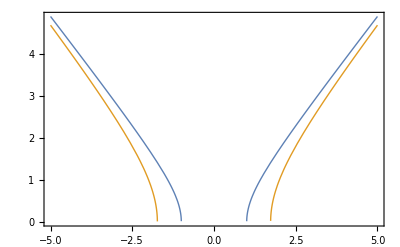

```mathematica
Plot[{Sqrt[x^2-1],Sqrt[x^2-3]},{x,-5,5},PlotStyle->Thick,Frame->True]
```

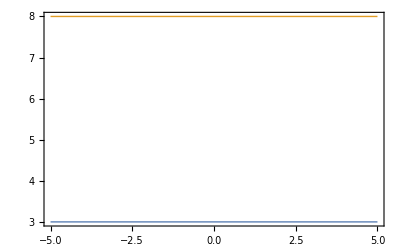

```mathematica
Plot[{3,8},{x,-5,5},PlotStyle->Thick,Frame->True]
```

```mathematica
Clear All
```

All Clear

### Ques 2 : xu_x+yu_y=u

The characteristic system is given by dx/x = dy/y = du/u and the characteristic equations are given by 
                                              y/x = c1  and  u/x = c2. 
Taking c1 = 1 and 3  and c2 = 3 and 8.

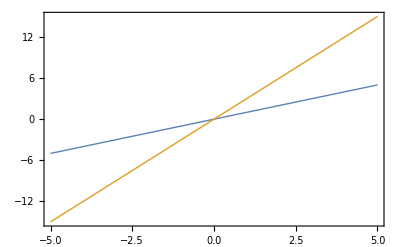

```mathematica
Plot[{x,3x},{x,-5,5},PlotStyle->Thick,Frame->True]
```

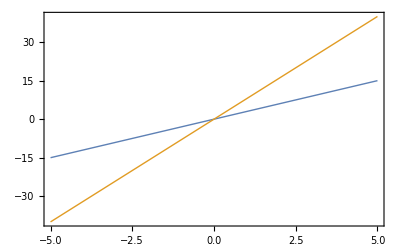

```mathematica
Plot[{3x,8x},{x,-5,5},PlotStyle->Thick,Frame->True]
```

### Ques 3 :(y+xu)u_x-(x+uy)u_y=x^2-y^2

The characteristic system is given by dx/(y+ux) = dy/-(x+uy) = du/(x^2-y^2) and the characteristic equations are given by 
                                              xy+u = c1  and  x^2+y^2-u^2 = c2. 
Taking c1 = 0 and 9  and c2 = 0 and 10.

```mathematica
Plot3D[{-x y,-x y+9},{x,-5,5},{y,-5,5},PlotStyle->Thick]
```

-Graphics3D-

```mathematica
Plot3D[{Sqrt[x^2+ y^2],Sqrt[x^2+y^2-10]},{x,-5,5},{y,-5,5},PlotStyle->Thick]
```

-Graphics3D-

### Ques 4 : y^2 u_x-xy u_y=x(u-2y)

The characteristic system is given by dx/y^2 = dy/-x y = du/x(u-2y) and the characteristic equations are given by 
                                              x^2+y^2= c1  and y-u= c2. 
Taking c1 = 2 and 5  and c2 = 5 and 7.

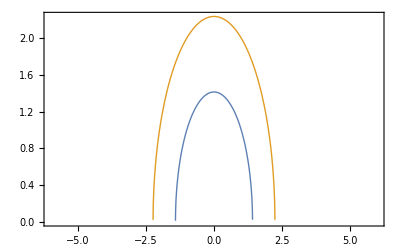

```mathematica
Plot[{Sqrt[2-x^2],Sqrt[5-x^2]},{x,-6,6},PlotStyle->Thick,Frame->True]
```

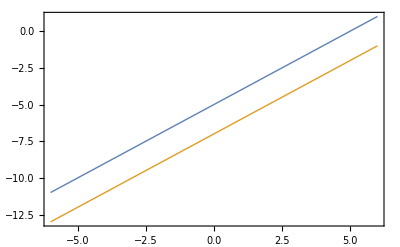

```mathematica
Plot[{y-5,y-7},{y,-6,6},PlotStyle->Thick,Frame->True]
```

### Ques 5 : u(x+y)u_x+ u(x-y)u_y= x^2+y^2

The characteristic system is given by dx/u(x+y) = dy/u(x-y) = du/(x^2+y^2) and the characteristic equations are given by 
                                              x^2/2 - y^2/2 - u = c1  and y^2 - u^2 - x^2 = c2. 
Taking c1 = 2 and 5  and c2 = 5 and 7.

```mathematica
Plot3D[{x^2-y^2/4,x^2-y^2-2/4},{x,-5,5},{y,-5,5},PlotStyle->Thick]
```

-Graphics3D-

```mathematica
Plot3D[{Sqrt[x^2-y^2],Sqrt[x^2-y^2+5]},{x,-5,5},{y,-5,5},PlotStyle->Thick]
```

-Graphics3D-

### Ques 6 :u_x-u_y= 1

The characteristic system is given by dx/1 = dy/(-1) = du/1 and the characteristic equations are given by 
                                              x-y = c1  and -y-u = c2. 
Taking c1 = 2 and 5  and c2 = 5 and 7.

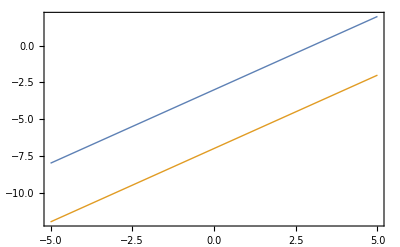

```mathematica
Plot[{x-3,x-7},{x,-5,5},PlotStyle->Thick, Frame -> True]
```

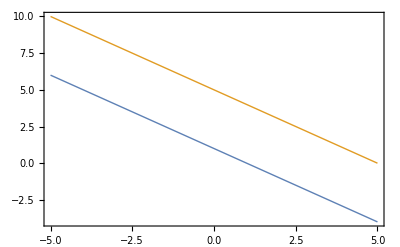

```mathematica
Plot[{1-y,5-y},{y,-5,5},PlotStyle->Thick, Frame -> True]
```

# PRACTICAL 8 : PLOT THE INTEGRAL SURFACES OF FIRST ORDER PARTIAL DIFFERENTIAL EQUATION WITH INITIAL DATA

## Ques : Solve the following first order partial differential equations and hence plot their integral surfaces.

### Ques 1 : xu_x+yu_y = 2 xy

```mathematica
pde1 = x* D[u[x,y],x]+y*D[u[x,y],y] == 2*x*y;
sol1 = DSolve[pde1,u[x,y],{x,y}]
```

{{u[x,y]→x y+C[1][y/x]}}

a. C[a] = Sin a

```mathematica
parsol1 = u[x,y]/.sol1[[1]]/.C[1][a_]->Sin[a]
```

x y+Sin[y/x]

```mathematica
Plot3D[parsol,{x,-8,8},{y,-8,8},AxesLabel->{x,y,u},Mesh->None,ColorFunction-> "Rainbow"]
```

-Graphics3D-

b. C[a] = Cos a

```mathematica
parsol = u[x,y]/.sol1[[1]]/.C[1][a_]->Cos[a]
```

x y+Cos[y/x]

```mathematica
Plot3D[parsol,{x,-8,8},{y,-8,8},AxesLabel->{x,y,u},Mesh->None,ColorFunction ->"Rainbow"]
```

-Graphics3D-

c. C[a] = a^3

```mathematica
parsol = u[x,y]/.sol1[[1]]/.C[1][a_]-> a^3
```

x y+y^3/x^3

```mathematica
Plot3D[parsol,{x,-8,8},{y,-8,8},AxesLabel->{x,y,u},Mesh->None,ColorFunction->"FuchsiaTones"]
```

-Graphics3D-

### Ques 2 : 3 u_x+2 u_y = 0

```mathematica
pde2 = 3* D[u[x,y],x]+2*D[u[x,y],y] == 0;
sol2 = DSolve[pde2,u[x,y],{x,y}]
```

{{u[x,y]→C[1][1/3 (-2 x+3 y)]}}

a. C[a] = Sin a

```mathematica
parsol2 = u[x,y]/.sol2[[1]]/.C[1][a_]->Sin[a]
```

Sin[1/3 (-2 x+3 y)]

```mathematica
Plot3D[parsol2,{x,-7,7},{y,-7,7},AxesLabel->{x,y,u},Mesh->None,ColorFunction-> "Rainbow"]
```

-Graphics3D-

b. C[a] = a^3

```mathematica
parsol2 = u[x,y]/.sol2[[1]]/.C[1][a_]-> a^3
```

1/27 (-2 x+3 y)^3

```mathematica
Plot3D[parsol2,{x,-8,8},{y,-8,8},AxesLabel->{x,y,u},Mesh->None,ColorFunction ->"Pastel"]
```

-Graphics3D-

c. C[a] = log a

```mathematica
parsol2 = u[x,y]/.sol2[[1]]/.C[1][a_]-> Log[a]
```

-ⅇ^y (-x+y)^3

```mathematica
Plot3D[parsol2,{x,-7,7},{y,-7,7},AxesLabel->{x,y,u},Mesh->None,ColorFunction-> "Rainbow"]
```

-Graphics3D-

### Ques 3 : u_x-u_y = 1

```mathematica
pde3 = D[u[x,y],x]-D[u[x,y],y] == 1;
sol3 = DSolve[pde3,u[x,y],{x,y}]
```

{{u[x,y]→x+C[1][x+y]}}

a. C[a] = Sin a

```mathematica
parsol3 = u[x,y]/.sol3[[1]]/.C[1][a_]->Sin[a]
```

x+Sin[x+y]

```mathematica
Plot3D[parsol3,{x,-8,8},{y,-8,8},AxesLabel->{x,y,u},Mesh->None,ColorFunction-> "Rainbow"]
```

-Graphics3D-

b. C[a] = Tan x

```mathematica
parsol3 = u[x,y]/.sol3[[1]]/.C[1][a_]-> Tan[x]
```

Sin[1/2 (-x^2+2 y)]

```mathematica
Plot3D[parsol3,{x,-2,2},{y,-2,2},AxesLabel->{x,y,u},Mesh->None,ColorFunction->"Aquamarine"]
```

-Graphics3D-

c. C[a] = e^a

```mathematica
parsol3 = u[x,y]/.sol3[[1]]/.C[1][a_]-> Exp[a]
```

Sin[1/2 (-x^2+2 y)]

```mathematica
Plot3D[parsol3,{x,0,2},{y,-2,2},AxesLabel->{x,y,u},Mesh->None,ColorFunction-> "Rainbow"]
```

-Graphics3D-